```mathematica
<<JLink`
```

```mathematica
AddToClassPath[FileNameJoin[{Nest[ParentDirectory,NotebookDirectory[],4], "artifacts","pack","lib"}]]
```

{C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Java\WolframSSH.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Java\WolframSSHKeyGen.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload\PacletManager\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload\PacletManager\Java\antlr.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload\PacletManager\Java\mexpr.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload\PacletManager\Java\mexprparser.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload\PacletManager\Java\PacletManager.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Autoload\PacletManager\Java\WRIjdbm.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\activation.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\bzip2.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\commons-codec-1.3.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\commons-collections-3.2.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\commons-httpclient-3.0.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\commons-lang-2.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\commons-logging-1.1.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\Convert.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\core-3.0.0.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\customizer.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\dom4j-1.6.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\Exif.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\externalservice.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\gnu-regexp-1.1.4.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\grib-8.0.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\jackcess-1.1.18.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\javase-3.0.0.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\jdbf.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\jdom.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\jmf.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\JPEG2000b.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\JSON.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\jxl.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\ldap.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\mail.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\mediaplayer.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\multiplayer.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\netcdf-4.2.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\poi-3.11-20150702.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\poi-examples-3.11-20150702.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\poi-excelant-3.11-20150702.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\poi-ooxml-3.11-20150702.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\poi-ooxml-schemas-3.11-20150702.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\poi-scratchpad-3.11-20150702.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\prefsAll.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\resourcesOptional.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\stax-api-1.0.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\tagsoup-1.0rc9.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\tar.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\xercesImpl.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\xml-apis.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\xmlbeans-2.3.0.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Converters\Java\zxing-client.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\bsf-Wolfram.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\bsf.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\concurrent.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\diva-canvas-core.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\GUIKit.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\OculusLayout.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\xercesImpl.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Packages\GUIKit\Java\xmlParserAPIs.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\commons-collections-3.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\commons-dbcp-1.2.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\commons-pool-1.2.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\derby.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\derbyclient.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\drizzle-jdbc-1.3.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\glazedlists.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\h2-1.3.174.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\h2-1.3.176.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\hsqldb.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\jaybird-full-2.2.9.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\jtds-1.3.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\mariadb-java-client-1.3.4.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\mysql-connector-java-5.1.38-bin.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\postgresql-9.4-1206-jdbc4.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\DatabaseLink\Java\sqlite-jdbc-3.8.11.2.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\jna.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\JRI.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\JRIEngine.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\log4j-1.2.16.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\REngine.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\RLink\Java\RLink.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\WebServices\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\WebServices\Java\commons-httpclient-3.0.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\WebServices\Java\commons-logging-1.0.4.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\WebServices\Java\junit-3.8.1.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\XMLSchema\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Links\XMLSchema\Java\commons-codec-1.3.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications\ClusterIntegration\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications\ClusterIntegration\Java\Wolfram_SGE.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications\DocumentationSearch\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications\LightweightGridClient\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications\LightweightGridClient\Java\wolfram-remote-services-client.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Components\Interpreter\Java\,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Components\Interpreter\Java\libphonenumber-7.0.4.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Components\Interpreter\Java\ParseTelephoneNumber.jar,C:\Program Files\Wolfram Research\Mathematica\10.4\SystemFiles\Java\Windows-x86-64\lib\tools.jar,C:\prog\nounou\artifacts\pack\lib\,C:\prog\nounou\artifacts\pack\lib\arpack_combined_all-0.1.jar,C:\prog\nounou\artifacts\pack\lib\breeze-macros_2.11-0.13-SNAPSHOT.jar,C:\prog\nounou\artifacts\pack\lib\breeze_2.11-0.13-SNAPSHOT.jar,C:\prog\nounou\artifacts\pack\lib\commons-codec-1.6.jar,C:\prog\nounou\artifacts\pack\lib\commons-io-2.4.jar,C:\prog\nounou\artifacts\pack\lib\commons-logging-1.1.3.jar,C:\prog\nounou\artifacts\pack\lib\commons-math3-3.2.jar,C:\prog\nounou\artifacts\pack\lib\core-1.1.2.jar,C:\prog\nounou\artifacts\pack\lib\gson-2.3.1.jar,C:\prog\nounou\artifacts\pack\lib\httpclient-4.3.6.jar,C:\prog\nounou\artifacts\pack\lib\httpcore-4.3.3.jar,C:\prog\nounou\artifacts\pack\lib\JavaEWAH-0.7.9.jar,C:\prog\nounou\artifacts\pack\lib\jsch-0.1.53.jar,C:\prog\nounou\artifacts\pack\lib\jtransforms-2.4.0.jar,C:\prog\nounou\artifacts\pack\lib\junit-4.8.2.jar,C:\prog\nounou\artifacts\pack\lib\machinist_2.11-0.4.1.jar,C:\prog\nounou\artifacts\pack\lib\nounou-core_2.11-0.7-SNAPSHOT.jar,C:\prog\nounou\artifacts\pack\lib\nounou-gui_2.11-0.7-SNAPSHOT.jar,C:\prog\nounou\artifacts\pack\lib\nounou-parent_2.11-0.7-SNAPSHOT.jar,C:\prog\nounou\artifacts\pack\lib\opencsv-2.3.jar,C:\prog\nounou\artifacts\pack\lib\org.eclipse.jdt.annotation-1.1.0.jar,C:\prog\nounou\artifacts\pack\lib\org.eclipse.jgit-4.1.1.201511131810-r.jar,C:\prog\nounou\artifacts\pack\lib\scala-library-2.11.8.jar,C:\prog\nounou\artifacts\pack\lib\scala-logging_2.11-3.4.0.jar,C:\prog\nounou\artifacts\pack\lib\scala-reflect-2.11.8.jar,C:\prog\nounou\artifacts\pack\lib\shapeless_2.11-2.2.5.jar,C:\prog\nounou\artifacts\pack\lib\slf4j-api-1.7.21.jar,C:\prog\nounou\artifacts\pack\lib\slf4j-simple-1.7.21.jar,C:\prog\nounou\artifacts\pack\lib\spire-macros_2.11-0.11.0.jar,C:\prog\nounou\artifacts\pack\lib\spire_2.11-0.11.0.jar}

```mathematica
JavaClassPath[]
```

```mathematica
class=LoadJavaClass["nounou.NN"]
```

JavaClass[nounou.NN,<>]

```mathematica
Methods[class]
```

static nounou.options.Opt[] convertOpt(nounou.options.Opt[], scala.reflect.ClassTag)
boolean equals(Object)
static nounou.elements.data.filters.NNFilterMedianSubtract filterMedianSubtract(nounou.elements.data.NNData)
Class getClass()
int hashCode()
static nounou.elements.NNElement[] load(String)
static nounou.elements.NNElement[] load(String[])
static com.typesafe.scalalogging.Logger logger()
static IllegalArgumentException loggerError(String, scala.collection.Seq)
static void loggerRequire(boolean, String, scala.collection.Seq) throws IllegalArgumentException
static nounou.ranges.NNRangeAll NNRangeAll()
static nounou.ranges.NNRangeAll NNRangeAll(int, int)
static nounou.ranges.NNRangeSpecifier NNRange(int[])
static nounou.ranges.NNRangeSpecifier NNRange(int[], int)
static nounou.ranges.NNRange NNRange(int, int, int, int)
static nounou.ranges.NNRangeTsEvent NNRangeTsEvent(java.math.BigInteger, int, int)
static nounou.ranges.NNRangeTsEvent NNRangeTsEvent(java.math.BigInteger, int, int, int)
static nounou.ranges.NNRangeTs NNRangeTs(java.math.BigInteger, java.math.BigInteger)
static nounou.ranges.NNRangeTs NNRangeTs(java.math.BigInteger, java.math.BigInteger, java.math.BigInteger)
void notify()
void notifyAll()
static nounou.elements.spikes.NNSpikes readSpikes(nounou.elements.data.NNDataChannel, java.math.BigInteger[], int, int)
static nounou.elements.spikes.NNSpikes readSpikes(nounou.elements.data.NNDataChannel, java.math.BigInteger[], scala.collection.Seq)
static nounou.elements.spikes.NNSpikes readSpikes(nounou.elements.data.NNData, java.math.BigInteger[], int[], int, int)
static nounou.elements.spikes.NNSpikes readSpikes(nounou.elements.data.NNData, java.math.BigInteger[], int, int, int)
static nounou.elements.spikes.NNSpikes readSpikes(nounou.elements.data.NNData, java.math.BigInteger[], int[], scala.collection.Seq)
static nounou.elements.spikes.NNSpikes readSpikes(nounou.elements.data.NNData, java.math.BigInteger[], int, scala.collection.Seq)
static void save(String, nounou.elements.NNElement)
static void save(String, nounou.elements.NNElement[])
static int[] spikeDetect(double[], scala.collection.Seq)
static java.math.BigInteger[] spikeDetect(nounou.elements.data.NNDataChannel, nounou.ranges.NNRangeSpecifier, scala.collection.Seq)
static java.math.BigInteger[] spikeDetect(nounou.elements.data.NNData, nounou.ranges.NNRangeSpecifier, int, scala.collection.Seq)
static double[] testArray()
static long[] toArray(breeze.linalg.DenseVector)
static String toString()
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
NN`toString[]
```

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

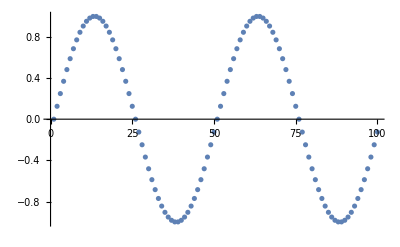

```mathematica
ListPlot[ NN`testArray[] ]
```